# Successioni e serie di funzioni

## Convergenza puntuale e uniforme di successioni

Data la successione di funzioni

f_n(t)=n^α t ⅇ^(-n t),  n = 1,..., ∞, t ∈  [0,+∞)

studiarne convergenza puntuale e unfirme nell’intervallo [0,+∞) al variare di α ∈ℝ

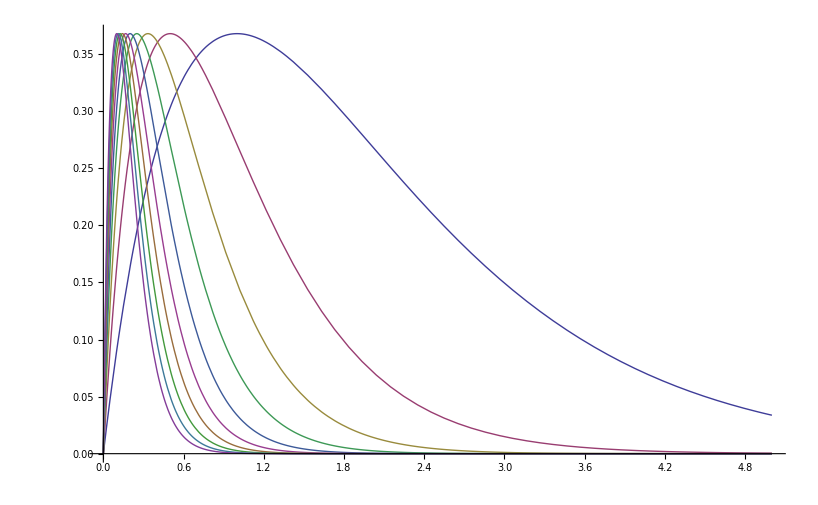

```mathematica
Plot[Evaluate[Table[n*t*Exp[-n*t],{n,1,10}]] , {t,0,5}]
```

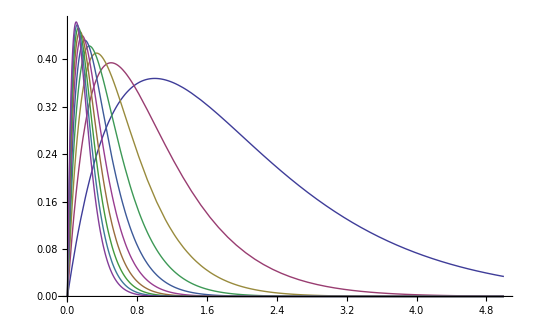

```mathematica
Plot[Evaluate[Table[n^(1.1)*t*Exp[-n*t],{n,1,10}]] , {t,0,5}]
```

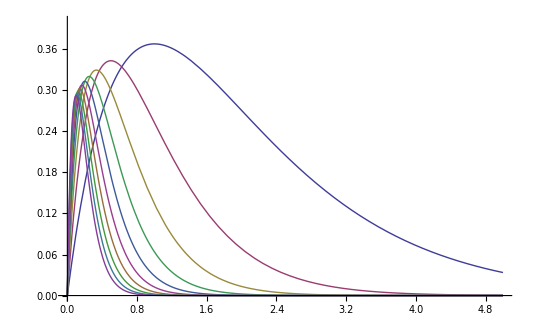

```mathematica
Plot[Evaluate[Table[n^(.9)*t*Exp[-n*t],{n,1,10}]] , {t,0,5}, PlotRange->{{0,5},{0,.4}}]
```

## Convergenza puntuale e uniforme di serie

Studiare la convergenza puntuale ed uniforme della serie

```mathematica
∑_(n=1)^∞ x^2/((x^2+1)^n),x ∈ℝ
```

Grafico dei termini della serie

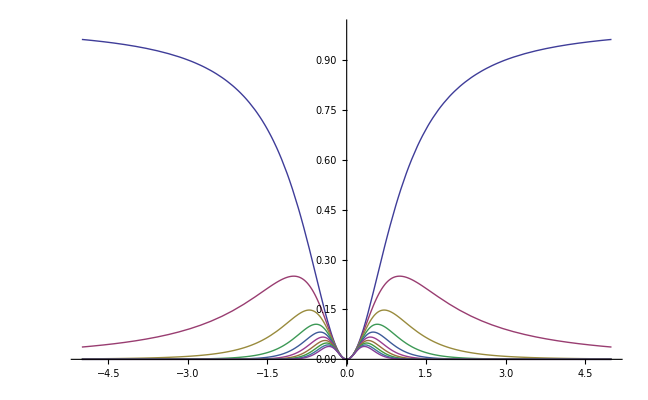

```mathematica
Plot[Evaluate[Table[x^2/(1+x^2)^n,{n,1,10}]] , {x,-5,5}, PlotRange->{{-5,5},{0,1}}]
```

Grafico delle somme parziali

```mathematica
∑_(n=0)^k x^2/((x^2+1)^n)=(x^2+1) (1-1/((x^2+1)^(k+1)))-x^2
```

e del limite puntuale della serie

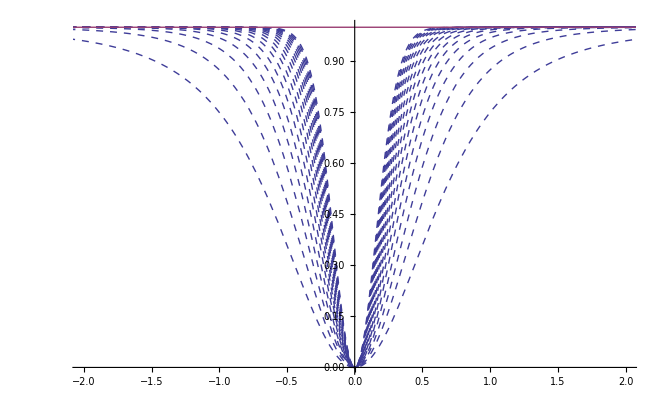

```mathematica
Plot[{Evaluate[Table[Sum[x^2/(1+x^2)^i, {i,1,n}],{n,2,20}]], 1}, {x,-4,4},PlotRange->{{-2,2},{0,1}}, PlotStyle->{Dashed, Thick}]
```

## Serie di Taylor

```mathematica
1/(x^2+1)=∑_(n=0)^∞ (-1)^n x^(2 n)
```

Raggio di convergenza R=1

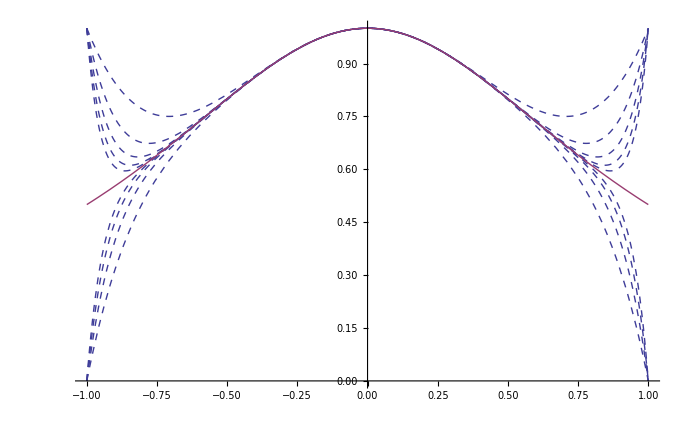

```mathematica
Plot[{Evaluate[Table[Sum[(-1)^i*x^(2*i), {i,0,n}],{n,2,10}]], 1/(1+x^2)} , {x,-1,1},PlotRange->{{-1,1},{0,1}}, PlotStyle->{Dashed, Thick}]
```

```mathematica
sin(x)=∑_(n=0)^∞ ((-1)^n x^(2 n+1))/((2 n+1)!)
```

Raggio di convergenza R=∞

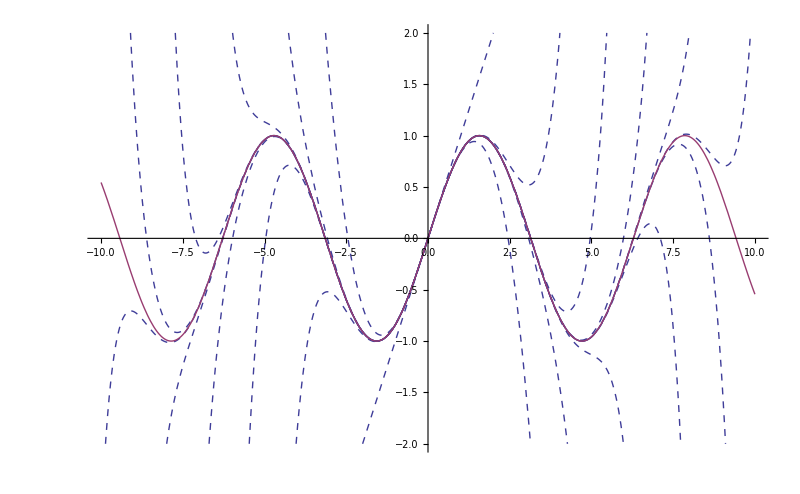

```mathematica
Plot[{Evaluate[Table[Sum[(-1)^i*x^(2*i+1)/Factorial[2*i+1], {i,0,n}],{n,0,10}]], Sin[x]} , {x,-10,10},PlotRange->{{-10,10},{0-2,2}}, PlotStyle->{Dashed, Thick}]
```

```mathematica
cos(x)=∑_(n=0)^∞ ((-1)^n x^(2 n))/((2 n)!)
```

Raggio di convergenza R=∞

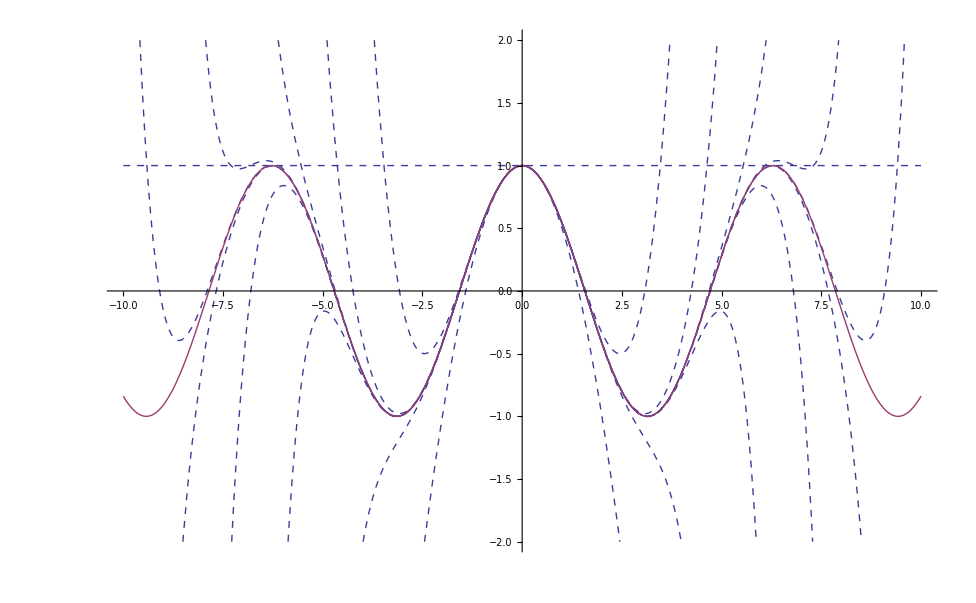

```mathematica
Plot[{Evaluate[Table[Sum[(-1)^i*x^(2*i)/Factorial[2*i], {i,0,n}],{n,0,10}]], Cos[x]} , {x,-10,10},PlotRange->{{-10,10},{0-2,2}}, PlotStyle->{Dashed, Thick}]
```

```mathematica
log(x)=∑_(n=1)^∞ ((-1)^(n+1) x^n)/n
```

Raggio di convergenza R=1

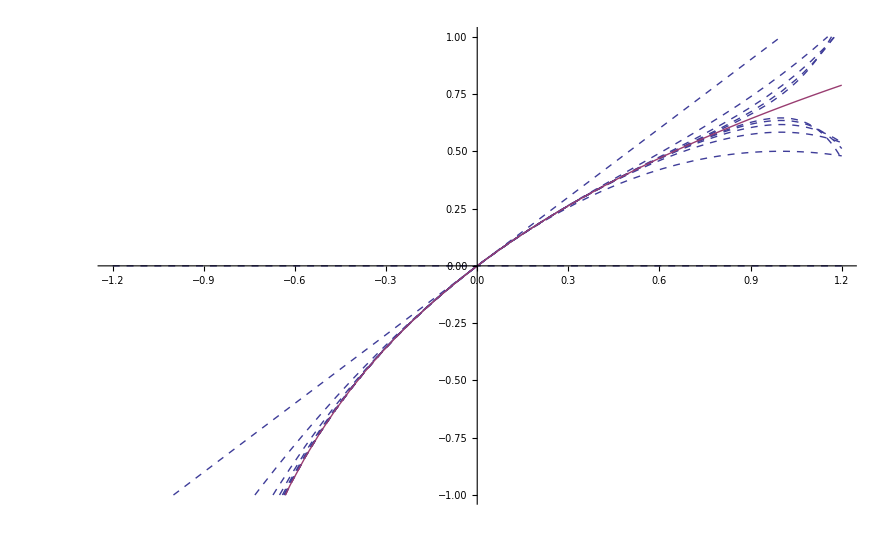

```mathematica
Plot[{Evaluate[Table[Sum[(-1)^(i+1)*x^(i)/i, {i,1,n}],{n,0,10}]], Log[1+x]} , {x,-1.2,1.2},PlotRange->{{-1.2,1.2},{-1,1}}, PlotStyle->{Dashed, Thick}]
```

```mathematica
√(x+1)=∑_(n=0)^∞ Binomial[1/2, n] x^n
```

Raggio di convergenza R= 1

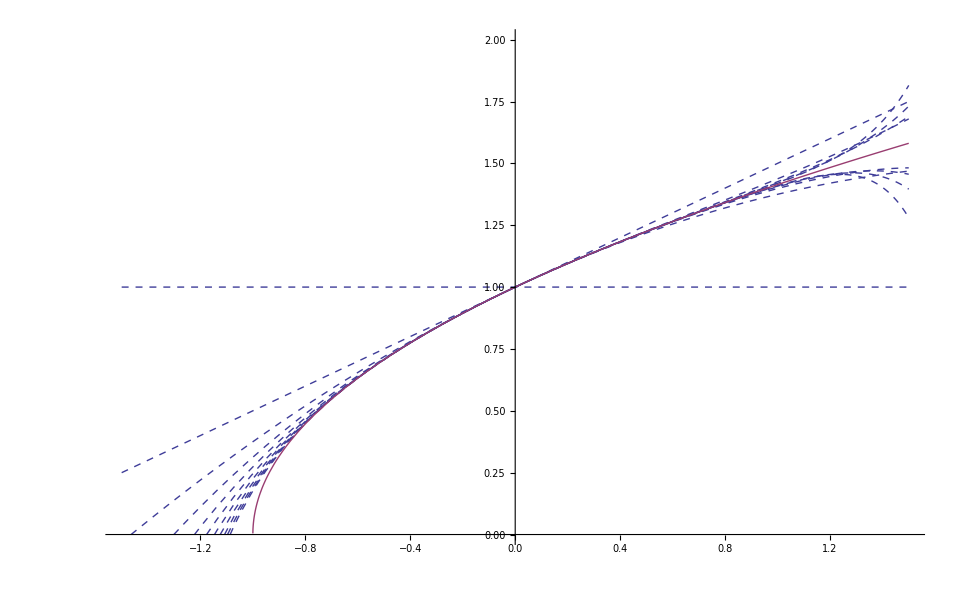

```mathematica
Plot[{Evaluate[Table[Sum[Binomial[1/2,i] *x^i, {i,0,n}],{n,0,10}]], Sqrt[1+x]} , {x,-1.5,1.5},PlotRange->{{-1.5,1.5},{0,2}}, PlotStyle->{Dashed, Thick}]
```

Esempio di funzione C^∞ ma non analitica

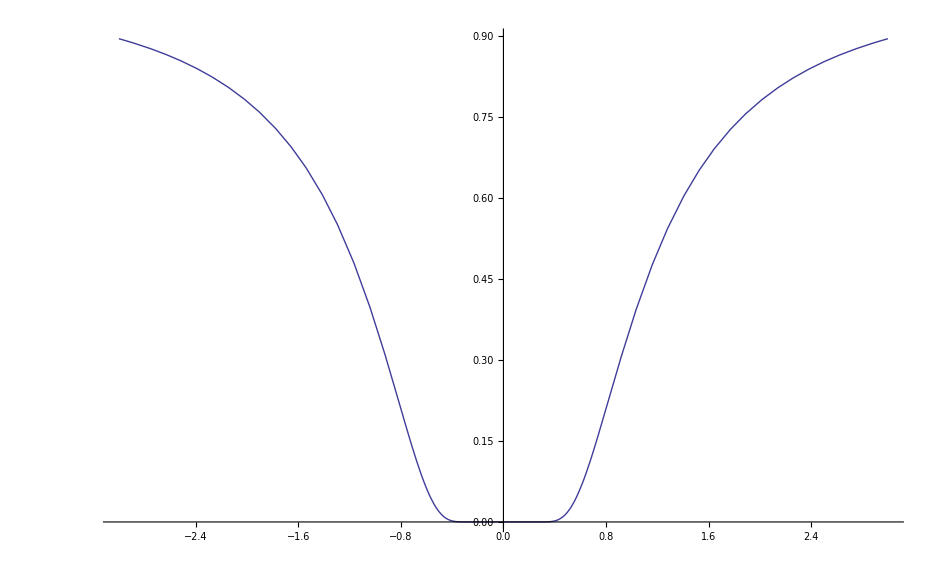

```mathematica
Plot[Exp[-1/x^2], {x,-3,3}]
```

## Serie di Fourier

Esempio di serie di Fourier lacunare

```mathematica
∑_(i=0)^(+∞) (cos(3^i x))/3^i
```

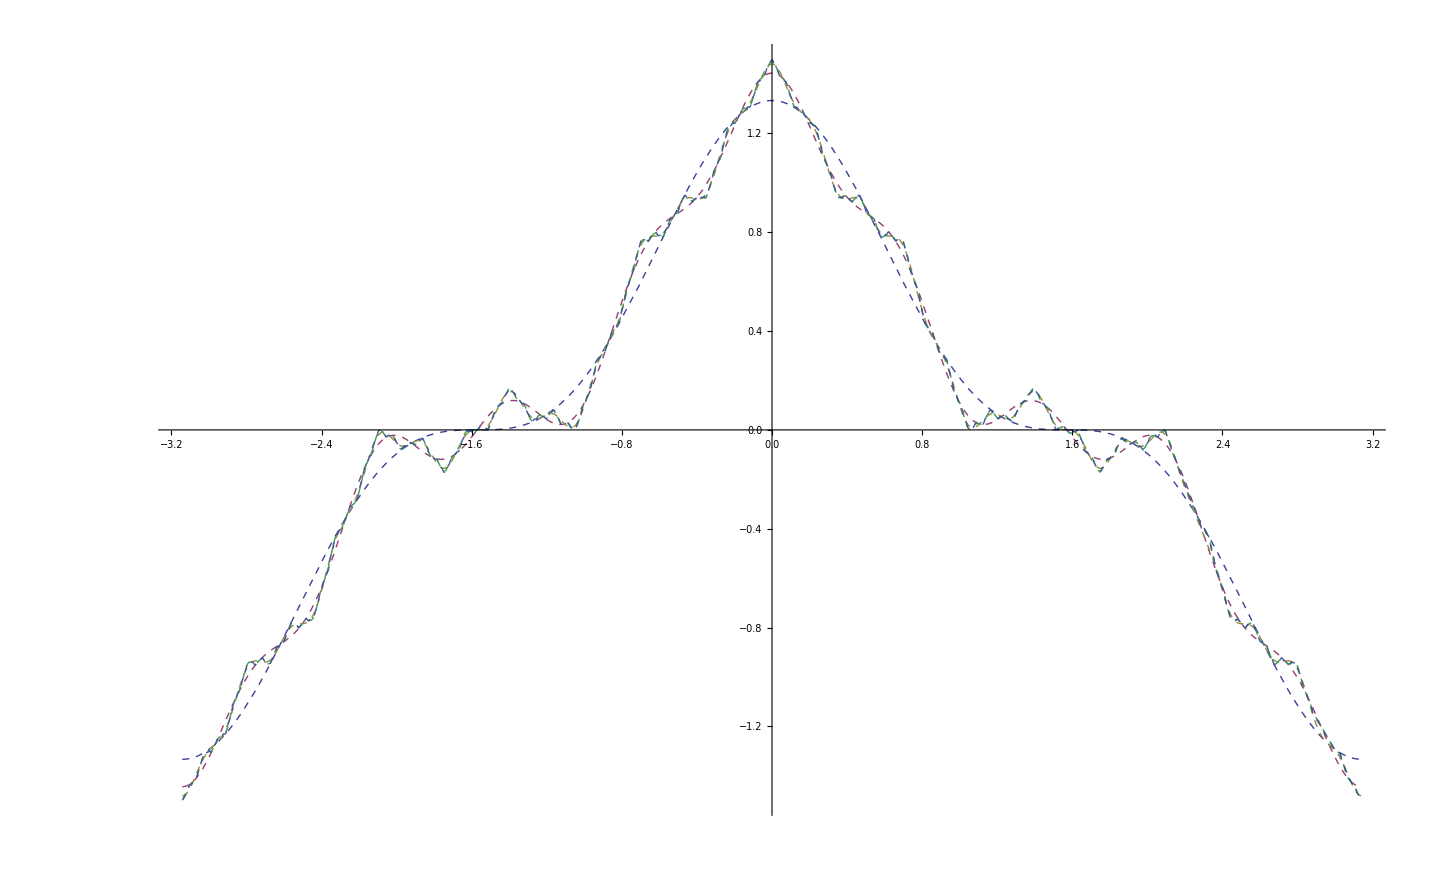

```mathematica
Plot[Evaluate[Table[Sum[ Cos[3^i*x]/3^i, {i,0,n}],{n,1,5}]] , {x,-π,π},PlotRange->{{-π,π},{-1.5,1.5}}, PlotStyle->{Dashed}]
```

## Applicazioni

### Risoluzione di equazioni differenziali

Le serie di potenze sono molto utile per ottenere approssimazioni di soluzioni di equazioni differenziali lineari a coefficienti polinomiali. Conderiamo per esempio l’equazione dell’oscillatore armonico (quantistico)

```mathematica
u''+(λ-x^2)u==0
```

In base alla sostituzione

```mathematica
u (x)=ⅇ^(-x^2/2) w(x)
```

siamo ricondotti all' equazione

```mathematica
w''-2 x w'+(λ-1) w=0
```

Ponendo poi

```mathematica
w (x)=∑_(n=0)^∞ Subscript[a, n] x^n
```

```mathematica
ricaviamo la relazione ricorsiva
```

```mathematica
a(n+2)==((2 n-1) a(n))/((n+2) (n+1))
```

```mathematica
coeff=RecurrenceTable[{a(n+2)==((2 n-λ+1) a(n))/((n+2) (n+1)),a(0)==1,a(1)==0},a,{n,100}];
```

```mathematica
coeff = RecurrenceTable[{a[n+2] == (2n+1)/((n+2)*(n+1))* a[n], a[0]==1, a[1] == 0}, a, {n,100}]
```

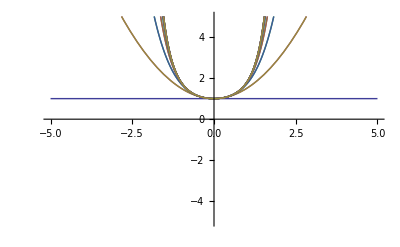

```mathematica
Plot[Evaluate[Table[Sum[  coeff[[i+1]]*x^i, {i,0,n}],{n,1,20}]] , {x,-5,5}, PlotRange->{{-5,5},{-5,5}}]
```

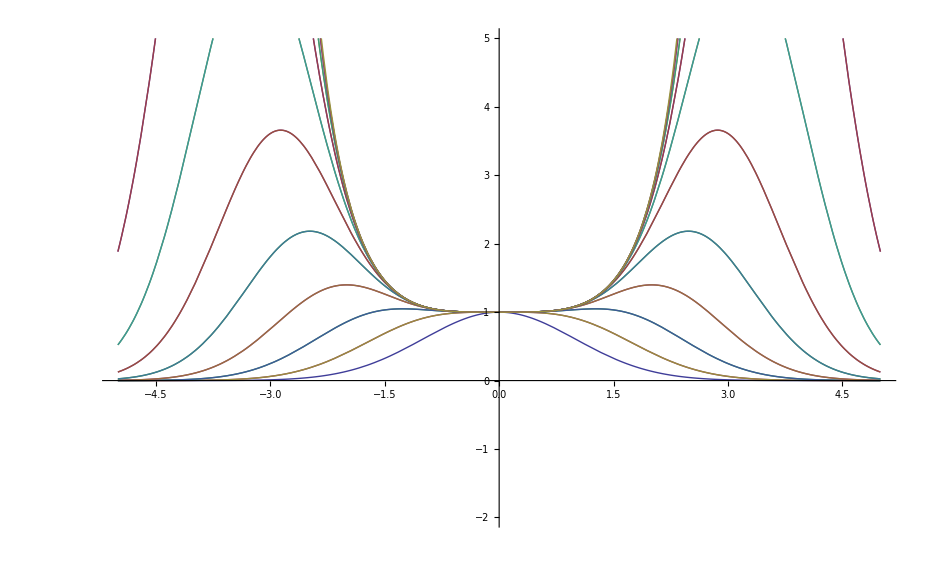

```mathematica
Plot[Evaluate[Table[Sum[ Exp[-x^2/2]* coeff[[i+1]]*x^i, {i,0,n}],{n,1,20}]] , {x,-5,5}, PlotRange->{{-5,5},{-2,5}}]
```

```mathematica
coeff = RecurrenceTable[{a[n+2]==(2*n+1-25)/((n+2)*(n+1))*a[n],a[0]==1,a[1]==0},a,{n,30}]
```

{1,0,-12,0,20,0,-32/3,0,16/7,0,-64/315,0,64/10395,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

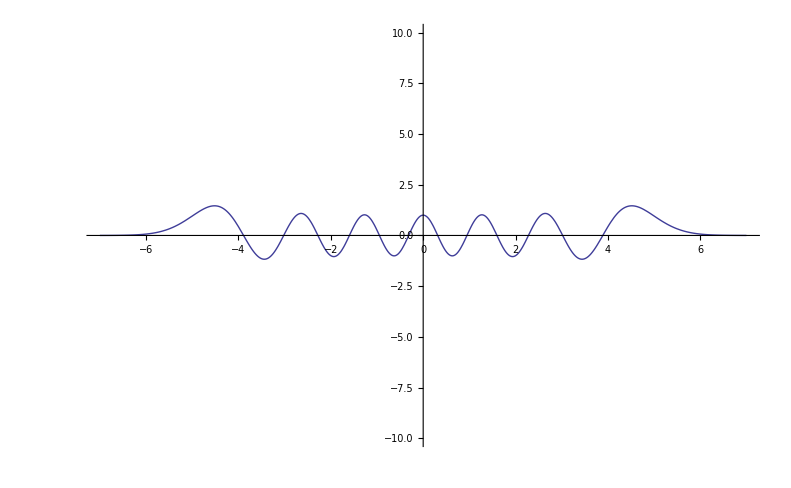

```mathematica
Plot[Evaluate[Sum[Exp[-x^2/2]*coeff[[i+1]]*x^i,{i,0,30}]],{x,-7,7},PlotRange->{{-7,7},{-10,10}}]
```

### Serie di Fourier e suoni

Serie di Fourier e onda lineare

```mathematica
Play[Sum[ (-1)^(n+1)*Sin[4π n*t]/n, {n,1,100}],{t,0,3}, SampleRate->32000]
```

-Graphics-

Quest’ultima è una serie di funzioni ma non una serie di Fourier (si vede bene controllando gli argomenti delle funzioni trigonometriche). Per maggiori informazioni, guardate: sound of hydrogen

```mathematica
Play[Evaluate[Sum[ Sin[440*2π(1-1/n^2)*t]+Sin[440*2π(1/4-1/(n+1)^2)*t]+Sin[440*2π(1/9-1/(n+2)^2)*t]+Sin[440*2π(1/16-1/(n+3)^2)*t]+Sin[440*2π(1/25-1/(n+4)^2)*t], {n,2,20}]],{t,0,10}, SampleRate->32000]
```

-Graphics-